```mathematica
bigyellow = {297413941736400589979939780692294751544,4,1};
```

```mathematica
bigred = {201412842028162214137229450141139961424,4,1};
```

```mathematica
cands =DeleteDuplicates@ ;ru = cands[[13]]; ca = getca[cands[[13]], 200];
```

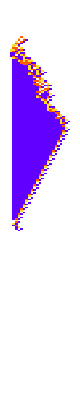
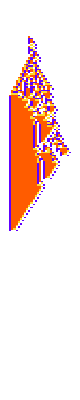
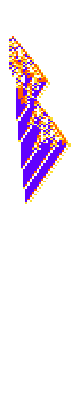
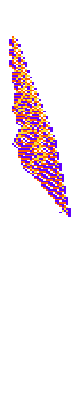
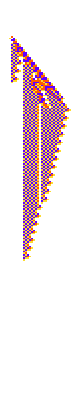
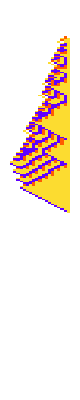
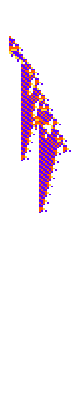
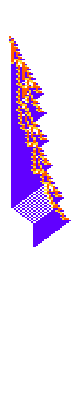

```mathematica
PlotCA/@ cands
```

```mathematica
SetOptions[ListPlot, PlotHighlighting->None];
```

## New Silhouette Functions

### Cleaner and Faster CAMask

#### Single ca

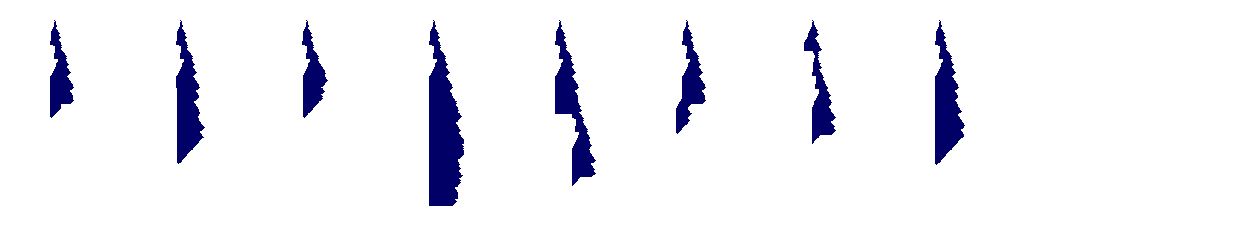

```mathematica
GraphicsRow[With[{ca =getca[ru, {200, {-50, 60}}]},  CAMask[#, "Color"->Darker[Blue, 0.6], "Trim"->{None, None}]& /@(PerturbCA[{ca, ru},#, "ReturnPerturbations"->False]&/@ RandomSample[allperts[ca], 10])]]
```

#### All perturbations merged

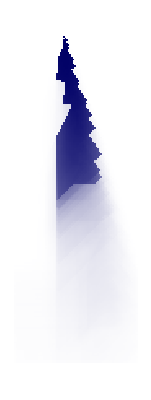

```mathematica
With[{ca =getca[cands[[13]], {200, {-30, 45}}]},  CAMask[PerturbCA[{ca, cands[[13]]},#, "ReturnPerturbations"->False]&/@ allperts[ca][[All]],  "Color"->Darker[Blue, 0.6], "Trim"->{None, None}]]
```

#### Other interesting rule

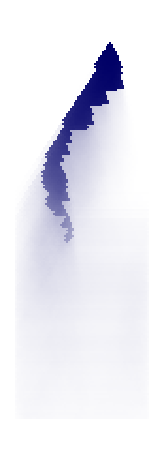

```mathematica
With[{ca =getca[ru, {200, {-50, 20}}]},  CAMask[PerturbCA[{ca, ru},#, "ReturnPerturbations"->False]&/@ allperts[ca],  "Color"->Darker[Blue, 0.6]]]
```

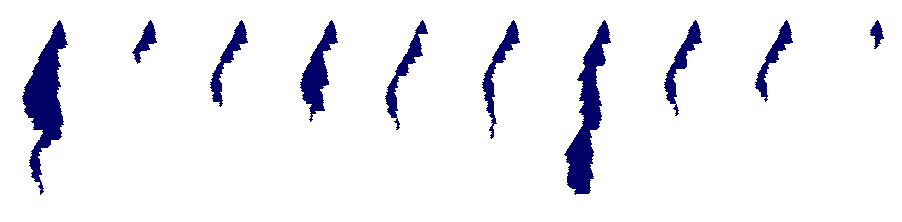

```mathematica
GraphicsRow[With[{ca =getca[cands[[9]], {200, {-60, 20}}]},  CAMask[#, "Color"->Darker[Blue, 0.6], "Trim"->{None, None}]& /@(PerturbCA[{ca, cands[[9]]},#, "ReturnPerturbations"->False]&/@ RandomSample[allperts[ca], 10])]]
```

TODO: Make mean plot more sensitive so you can see the perturbations more (Try Log?)

### Polygon version

#### Multi-color

```mathematica
SeedRandom[1238];
cols = RandomSample[ColorData["BrightBands", "ColorFunction"][#]&/@ Table[i, {i, 0, 1, .1}], 10];
```

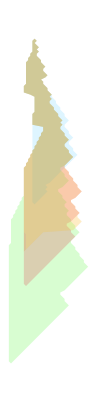

```mathematica
Show@@Table[Graphics[{Opacity[0.2,cols[[Mod[i+9, 10]+1]]], CAPolygon[PerturbCA[ru, "ReturnPerturbations"->False]]}], {i, 5}]
```

#### 3D Stack (Fossil drawer)

```mathematica
Graphics3D[MapIndexed[(*Style[*)CAPolygon[#1, 5#2[[1]]](*,Blend[Lighter/@RGBColor/@{Hue[0.58, 1., 0.76],Hue[0.77, 0.78, 0.9],Hue[0.02, 1., 1.],Hue[0.08, 1., 1.]}, #2[[1]]/50]] *)&,ReverseSortBy[Table[PerturbCA[ru, "ReturnPerturbations"->False], 10], TestCALifeTime]]]
```

-Graphics3D-

### Overlayed Polygon on all candidates

```mathematica
ParallelMap[(Show@@Table[Graphics[{Opacity[0.05,Lighter[Red]], CAPolygon[PerturbCA[ru, "ReturnPerturbations"->False]]}], {i, 100}]&), cands]
```

```mathematica
Show@@Table[PlotSilhouette[#, "Perturbation"->1, "Opacity"->0.05, "Color"->Lighter[Red]], {i, 100}]&/@ cands
```

-Graphics-

#### Overlayed outline

```mathematica
Show@@Table[ShowOutline[cands[[13]], "Perturbation"->1,"Opacity"->0.3,"Color"->ColorData["Rainbow"][RandomReal[]]], {i, 5}]
```

-Graphics-

#### Single

```mathematica
Graphics[{Lighter[Blue], CAPolygon[ca]}]
```

-Graphics-

## Comparing Widths With Lifetimes at all steps

```mathematica
pcas = Block[{ru = {299459058088077823758143088095350287424,4,1}},
ca = getca[ru];
pcas = Flatten[PerturbAll[{ca, ru}, #]&/@ Flatten[bodyidxs[ca], 1], 1]];
```

```mathematica
l = Length[pcas];
```

```mathematica
lts = TestCALifeTime/@pcas;
```

```mathematica
shapes = Map[nonzeroRange, pcas, {2}];
```

```mathematica
widths = Map[If[# == {}, 0,Abs[ Subtract@@#]+1]&,  shapes, {2}];
```

```mathematica
cs = Counts[shapes];
```

```mathematica
GraphicsGrid[Partition[Table[Labeled[ListPlot[Transpose[{widths[[All, i]], lts}], PlotHighlighting->None],"Step: "<>ToString[i]], {i, 5, TestCALifeTime[ca], 5}], 5]]
```

## Predicting Lifetime Based on Width

#### Step 70

```mathematica
SeedRandom[4455];
trainidxs = Sort[RandomSample[Range[Length[lts]], 3000]];
testidxs =  Complement[Range[Length[lts]], trainidxs];
```

```mathematica
pf70 = Predict[Thread[widths[[trainidxs, 70]]->(lts[[trainidxs]]/.-Infinity->300)]]
```

PredictorFunction[…]

```mathematica
GraphicsRow[ListPlot[#, PlotHighlighting->None, PlotRange->210]&/@{Thread[pf70[widths[[testidxs, 70]]]], lts[[testidxs]]}]
```

-Graphics-

Loss

```mathematica
ListPlot[Abs[#2 - #1]&@@@Transpose[{Thread[pf70[widths[[testidxs, 100]]]], lts[[testidxs]]}], PlotRange->All]
```

-Graphics-

#### Step 100

```mathematica
pf100 = Predict[Thread[widths[[trainidxs, 100]]->(lts[[trainidxs]]/.-Infinity->300)]]
```

PredictorFunction[…]

```mathematica
GraphicsRow[ListPlot[#, PlotHighlighting->None, PlotRange->300]&/@{Thread[pf100[widths[[testidxs, 100]]]], (lts[[testidxs]]/.-Infinity->300)}]
```

-Graphics-

Loss

```mathematica
ListPlot[Abs[#2 - #1]&@@@Transpose[{Thread[pf100[widths[[testidxs, 100]]]], lts[[testidxs]]}], PlotRange->All]
```

-Graphics-

#### Step 30

```mathematica
pf30 = Predict[Thread[widths[[trainidxs, 30]]->(lts[[trainidxs]]/.-Infinity->300)]]
```

PredictorFunction[…]

```mathematica
GraphicsRow[ListPlot[#, PlotHighlighting->None, PlotRange->300]&/@{Thread[pf30[widths[[testidxs, 30]]]], (lts[[testidxs]]/.-Infinity->300)}]
```

-Graphics-

Loss

```mathematica
ListPlot[Abs[#2 - #1]&@@@Transpose[{Thread[pf30[widths[[testidxs, 30]]]], lts[[testidxs]]}], PlotRange->All]
```

-Graphics-

## Predicting based on row sequence

```mathematica
rows = pcas[[trainidxs, 100]];
```

```mathematica
pfrow = Predict[Thread[rows->(lts[[trainidxs]]/.-Infinity->300)]]
```

PredictorFunction[…]

```mathematica
GraphicsRow[ListPlot[#, PlotHighlighting->None, PlotRange->300]&/@{Thread[pfrow[pcas[[testidxs, 100]]]],(lts[[testidxs]]/.-Infinity->300)}]
```

-Graphics-

```mathematica
pfrow[Table[0, Length[ca[[1]]]]]
pfrow[ca[[100]]]
```

30.0638

28.1358

Loss

```mathematica
ListPlot[Abs[#2 - #1]&@@@Transpose[{Thread[pfrow[pcas[[testidxs, 100]]]], lts[[testidxs]]}], PlotRange->All]
```

-Graphics-

#### Step 30

```mathematica
rows = pcas[[trainidxs, 30]];
```

```mathematica
pfrow30 = Predict[Thread[rows->(lts[[trainidxs]]/.-Infinity->300)]]
```

PredictorFunction[…]

```mathematica
GraphicsRow[ListPlot[#, PlotHighlighting->None, PlotRange->300]&/@{Thread[pfrow30[pcas[[testidxs, 30]]]], (lts[[testidxs]]/.-Infinity->300)}]
```

-Graphics-

Loss

```mathematica
ListPlot[Abs[#2 - #1]&@@@Transpose[{Thread[pfrow30[pcas[[testidxs, 30]]]], lts[[testidxs]]}], PlotRange->All]
```

-Graphics-

```mathematica
pfrow[Table[0, Length[ca[[1]]]]]
pfrow[ca[[100]]]
```

86.1602

116.182

## Predicting Lifetime Based on Non-Zero Range sequence

```mathematica
SeedRandom[4456];
trainidxs = Sort[RandomSample[Range[Length[lts]], 3000]];
testidxs =  Complement[Range[Length[lts]], trainidxs];
```

```mathematica
getnzseqs[ca_,row_,  idxs_]:= Module[{left, right, rows},
{left, right} = gettrimoffsets[ca, {1, None}][[1]];
rows = pcas[[idxs, row]];
MapThread[#1[[ #2[[1]];;#2[[2]]]]&, {rows, (If[# =={}, {left, right}, #]&/@(nonzeroRange/@rows))}]];
```

```mathematica
nzseqstrain = getnzseqs[ca,30, trainidxs];
```

```mathematica
pfseq = Predict[Thread[nzseqstrain->(lts[[trainidxs]]/.-Infinity->300)]]
```

PredictorFunction[…]

```mathematica
GraphicsRow[ListPlot[#, PlotHighlighting->None, PlotRange->300]&/@{Thread[pfseq[getnzseqs[ca,30, testidxs]]], (lts[[testidxs]]/.-Infinity->300)}]
```

-Graphics-

```mathematica
ListPlot[Abs[#2 - #1]&@@@Transpose[{Thread[pfseq[getnzseqs[ca,30, testidxs]]], lts[[testidxs]]}], PlotRange->All]
```

-Graphics-

## Predicting Widths based on previous widths

```mathematica
getcoords[ca_]:=MapIndexed[<|"left"->{#1[[1]], Length[ca] -#2[[1]]},"right"-> {#1[[2]], Length[ca] -#2[[1]]}|>&, TakeWhile[nonzeroRange/@ca, #!={}&]]
```

```mathematica
Values/@getcoords[ca]
```

{{{201,200},{201,200}},{{202,199},{202,199}},{{201,198},{203,198}},{{201,197},{202,197}},{{201,196},{203,196}},{{201,195},{204,195}},{{201,194},{203,194}},{{201,193},{204,193}},{{200,192},{203,192}},{{200,191},{203,191}},{{199,190},{204,190}},{{199,189},{205,189}},{{198,188},{205,188}},{{198,187},{206,187}},{{198,186},{207,186}},{{198,185},{206,185}},{{198,184},{206,184}},{{198,183},{207,183}},{{198,182},{208,182}},{{198,181},{207,181}},{{198,180},{205,180}},{{198,179},{206,179}},{{198,178},{206,178}},{{197,177},{207,177}},{{197,176},{208,176}},{{197,175},{208,175}},{{197,174},{209,174}},{{200,173},{210,173}},{{202,172},{209,172}},{{202,171},{210,171}},{{202,170},{209,170}},{{202,169},{209,169}},{{202,168},{210,168}},{{202,167},{211,167}},{{202,166},{211,166}},{{202,165},{212,165}},{{201,164},{213,164}},{{201,163},{213,163}},{{201,162},{214,162}},{{201,161},{215,161}},{{201,160},{214,160}},{{201,159},{215,159}},{{206,158},{214,158}},{{206,157},{214,157}},{{206,156},{215,156}},{{205,155},{216,155}},{{205,154},{216,154}},{{204,153},{217,153}},{{204,152},{218,152}},{{203,151},{217,151}},{{203,150},{216,150}},{{202,149},{216,149}},{{202,148},{217,148}},{{201,147},{218,147}},{{201,146},{218,146}},{{200,145},{219,145}},{{200,144},{220,144}},{{199,143},{219,143}},{{199,142},{218,142}},{{198,141},{217,141}},{{198,140},{216,140}},{{197,139},{216,139}},{{197,138},{217,138}},{{197,137},{218,137}},{{197,136},{218,136}},{{197,135},{219,135}},{{197,134},{220,134}},{{197,133},{220,133}},{{197,132},{221,132}},{{197,131},{222,131}},{{197,130},{222,130}},{{197,129},{223,129}},{{197,128},{224,128}},{{197,127},{223,127}},{{197,126},{222,126}},{{197,125},{221,125}},{{197,124},{219,124}},{{197,123},{219,123}},{{197,122},{220,122}},{{197,121},{221,121}},{{197,120},{221,120}},{{197,119},{222,119}},{{197,118},{223,118}},{{197,117},{222,117}},{{197,116},{222,116}},{{197,115},{223,115}},{{197,114},{224,114}},{{197,113},{223,113}},{{197,112},{222,112}},{{197,111},{221,111}},{{197,110},{220,110}},{{197,109},{206,109}},{{197,108},{205,108}},{{197,107},{204,107}},{{197,106},{203,106}},{{197,105},{202,105}},{{197,104},{201,104}},{{197,103},{200,103}},{{197,102},{199,102}},{{197,101},{198,101}},{{197,100},{197,100}}}

```mathematica
shaperus = Thread[shapes[[All, ;;30]]->shapes[[All, 31;;]]];
```

```mathematica
widthrus = Thread[widths[[trainidxs, ;;30]]->widths[[trainidxs, 31;;]]];
```

```mathematica
widthrus[[1]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}→{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
pfwidths = Predict[widthrus];
```

#### Click to copy ideas

```mathematica
Block[{nets={},rounds=4000},
NetTrain[NetChain[{6,ElementwiseLayer["SELU"],6,ElementwiseLayer["SELU"],6,ElementwiseLayer["SELU"],{}},"Input"->"Real"],Thread[#->Sin[#]]&@Range[0,10,0.1],MaxTrainingRounds->rounds,TrainingProgressFunction->{AppendTo[nets,#Round->#Net]&,"Interval"->Quantity[rounds/4,"Rounds"]}];
GraphicsRow[Labeled[Plot[{Sin[x],#[[2]][x]},{x,0,15},PlotRange->{-2.5,2.5},PlotRangePadding->None,PlotStyle->{Automatic,Red},Frame->True,FrameTicks->None,AspectRatio->1/2.5,Prolog->{GrayLevel[.8,.2],Rectangle[{10,-2.5},{15,2.5}]}],StringTemplate["`` rounds"][#[[1]]],Spacings->{0,0},ImageMargins->{{Automatic,Automatic},{Scaled[.01],Scaled[.01]}}]&/@nets,ImageSize->Full,Spacings->10]
]
```

```mathematica
cacolor[0,{p0_,p1_,___}]:=Blend[{Blend[{LightCyan,Blue},p1],Pink},1-p0]
```

```mathematica
cacolorprob[1,{p0_,p1_,___}]:=Blend[RGBColor/@{GrayLevel[0.8, 0.2],Hue[0.09, 1., 0.9],Hue[1, 1., 0.87]},p1]
```

```mathematica
cacolorprob[0,{p0_,p1_,___}]:=Blend[RGBColor/@{GrayLevel[0.8, 0.2],Hue[0.06, 0.45, 0.9500000000000001],Hue[0.07, 0.6900000000000001, 0.93]},p1]
```

```mathematica
ClearAll@cadpix
```

```mathematica
cadpix[carule_,caNet_,seed_,colfun_:cacolor]:=Module[{ca},SeedRandom[seed];ca=CellularAutomaton[carule,{{1}, 0},200];ArrayPlot[Join[Take[ca,64]/.{1->Black,0->White},MapThread[colfun,{Take[ca,-64],NetChain[{NetExtract[caNet,"encoder"],NetExtract[caNet,"decoder"]}][1+Take[ca,30]]},2]],PixelConstrained->1,FrameStyle->GrayLevel[.75]]]
```

```mathematica
net=CloudGet[CloudObject["https://www.wolframcloud.com/obj/7dfdea56-0000-4445-8035-6d8a8ff27a70"]]
```

NetGraph[<3>, <5>]

```mathematica
GraphicsGrid[Partition[Table[cadpix[<|"OuterTotalisticCode"->600,"Range"->2|>,net,seed,cacolorprob],{seed,4900,4921}],7],ImageSize->493,Spacings->{5,5}]
```

```mathematica
o = cadpix[ru,net,4900,cacolorprob];
```

## Fixing bugs

```mathematica
Select[]
```

```mathematica
PlotCA[{PerturbCA[ru, <|{30, 210}->0|>, "Steps"->500],<|{30, 210}->0|>}]
```

-Graphics-

```mathematica
ru
```

{299459058088077823758143088095350287424,4,1}

Fixed width

```mathematica
PerturbCA[getca[{299459058088077823758143088095350287424,4,1}]]
```

```mathematica
cas = Table[PlotCA[PerturbCA[ru]], 10];
```

```mathematica
Table[PerturbCA[ru, "ReturnPerturbations"->False], 10]
```

```mathematica
Graph[{1 <-> 2, 2 <-> 3, 
  3 <-> 1}, VertexShapeFunction -> (Inset[-Graphics-, #1, Center, 2*#3] &), 
 VertexSize -> .2]
```

```mathematica
FeatureExtract
```

```mathematica
FindClusters[]
```

```mathematica
Graph[{1 <-> 2, 2 <-> 3, 
  3 <-> 1}, VertexShape -> -Graphics-, VertexSize -> .2]
```

```mathematica
Graph[{1 <-> 2, 2 <-> 3, 
  3 <-> 1}, VertexShapeFunction -> (Inset[Text[#3], #1, Center, 2*#3] &), 
 VertexSize -> .1]
```

-Graphics-

### Steps bug

```mathematica
aps = allperts[ru]
```

```mathematica
PlotCA[{299459058088077823758143088095350287424,4,1}]
```

-Graphics-

```mathematica
aps = allperts[CellularAutomaton[ru,{{1}, 0}, {500, All}], 4];
```

```mathematica
TestCALifeTime[PerturbCA[{CellularAutomaton[ru,{{1}, 0}, {500, All}], ru}, #]]&/@ RandomSample[aps, 100]
```

{64,136,46,157,117,107,100,93,35,45,189,100,178,100,49,111,101,167,110,195,118,105,89,100,106,120,113,114,118,101,138,107,105,104,173,111,122,281,129,100,100,101,252,56,199,106,46,127,113,260,35,122,117,349,122,101,149,123,184,106,122,118,101,107,100,107,100,34,129,103,58,102,89,91,100,100,106,47,98,125,101,107,145,100,255,186,107,110,107,208,109,100,104,138,87,53,67,212,172,107}

```mathematica
ru
```

{299459058088077823758143088095350287424,4,1}

```mathematica
lts500 = Block[{ru = {299459058088077823758143088095350287424,4,1}, ca, aps},
ca = CellularAutomaton[ru,{{1}, 0}, {500, All}];
aps  = allperts[ca, ru[[2]]];
ParallelMap[TestCALifeTime[PerturbCA[{ca, ru}, #]]&, RandomSample[aps, 100]]]
```

{182,130,173,101,188,65,107,80,240,138,89,107,106,101,101,106,190,193,122,171,6,122,100,100,192,171,120,22,4,101,101,58,101,149,124,100,113,106,111,100,100,100,107,118,101,189,107,106,101,113,122,106,161,63,152,219,61,123,167,135,191,135,112,100,31,115,117,115,133,192,39,131,100,117,70,61,191,106,90,189,122,43,132,128,103,106,100,74,119,105,100,102,107,87,126,39,125,107,77,136}

## Adaptive Therapy

```mathematica
getcancerperts[ru]
```

{<|{11,202}→0|>,<|{12,205}→1|>,<|{16,201}→0|>,<|{19,204}→0|>,<|{19,208}→3|>,<|{20,204}→1|>,<|{20,205}→2|>,<|{22,201}→3|>,<|{29,208}→0|>,<|{30,209}→1|>,<|{33,204}→0|>,<|{33,206}→2|>,<|{33,207}→0|>,<|{33,207}→2|>,<|{33,209}→1|>,<|{34,207}→2|>,<|{34,208}→1|>,<|{35,204}→1|>,<|{35,205}→3|>,<|{35,208}→2|>,<|{35,209}→0|>,<|{35,209}→1|>,<|{36,209}→0|>,<|{36,209}→2|>,<|{37,207}→1|>,<|{37,210}→1|>,<|{39,209}→3|>,<|{40,213}→1|>,<|{41,202}→3|>,<|{41,212}→0|>,<|{44,210}→0|>,<|{47,211}→3|>,<|{48,209}→0|>,<|{48,213}→0|>,<|{48,214}→0|>,<|{48,216}→3|>,<|{49,215}→1|>,<|{49,215}→3|>,<|{50,203}→2|>,<|{50,208}→0|>,<|{50,210}→1|>,<|{50,216}→1|>,<|{51,204}→0|>,<|{51,205}→3|>,<|{51,210}→3|>,<|{51,212}→0|>,<|{52,211}→0|>,<|{52,216}→3|>,<|{53,203}→0|>,<|{53,204}→3|>,<|{53,207}→3|>,<|{53,208}→1|>,<|{54,204}→3|>,<|{54,207}→1|>,<|{54,209}→0|>,<|{54,214}→3|>,<|{54,215}→3|>,<|{54,217}→3|>,<|{55,209}→1|>,<|{56,210}→0|>,<|{56,215}→0|>,<|{56,217}→0|>,<|{57,206}→1|>,<|{57,207}→1|>,<|{57,209}→0|>,<|{57,209}→1|>,<|{57,220}→0|>,<|{57,220}→3|>,<|{58,201}→3|>,<|{58,202}→3|>,<|{58,205}→2|>,<|{58,208}→2|>,<|{58,210}→0|>,<|{58,211}→2|>,<|{58,219}→0|>,<|{58,219}→3|>,<|{59,202}→1|>,<|{59,202}→2|>,<|{59,212}→3|>,<|{59,218}→0|>,<|{59,218}→3|>,<|{60,200}→1|>,<|{60,209}→0|>,<|{60,217}→0|>,<|{61,198}→1|>,<|{61,199}→3|>,<|{61,216}→0|>,<|{62,200}→3|>,<|{62,207}→3|>,<|{62,212}→3|>,<|{62,213}→3|>,<|{62,216}→3|>,<|{63,209}→1|>,<|{64,202}→3|>,<|{64,205}→3|>,<|{64,210}→0|>,<|{64,212}→3|>,<|{65,206}→3|>,<|{65,214}→3|>,<|{66,200}→3|>,<|{66,201}→3|>,<|{66,211}→3|>,<|{67,208}→3|>,<|{67,210}→3|>,<|{68,203}→3|>,<|{68,217}→0|>,<|{68,218}→0|>,<|{69,204}→3|>,<|{69,207}→3|>,<|{69,212}→0|>,<|{69,214}→0|>,<|{69,216}→0|>,<|{69,217}→0|>,<|{69,218}→3|>,<|{69,219}→0|>,<|{70,216}→1|>,<|{70,222}→0|>,<|{71,206}→3|>,<|{71,212}→3|>,<|{71,214}→0|>,<|{72,215}→1|>,<|{72,223}→2|>,<|{73,199}→3|>,<|{73,216}→3|>,<|{73,222}→3|>,<|{73,223}→3|>,<|{74,210}→3|>,<|{74,220}→3|>,<|{74,222}→3|>,<|{75,197}→3|>,<|{75,211}→3|>,<|{75,212}→3|>,<|{75,219}→1|>,<|{76,199}→3|>,<|{76,210}→3|>,<|{78,197}→3|>,<|{79,199}→3|>,<|{79,214}→3|>,<|{79,218}→1|>,<|{80,219}→3|>,<|{81,197}→3|>,<|{81,216}→3|>,<|{81,217}→1|>,<|{82,218}→1|>,<|{83,217}→1|>,<|{83,219}→3|>,<|{83,221}→1|>,<|{85,199}→3|>,<|{86,220}→3|>,<|{87,197}→3|>,<|{88,216}→1|>,<|{89,217}→3|>,<|{91,219}→3|>,<|{96,198}→3|>,<|{100,197}→3|>,<|{101,197}→1|>}

```mathematica
PlotCA[PerturbCA[ru, #]]&/@ RandomSample[%181, 10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
pca = PerturbCA[ru, <|{11,202}->0|>];
aps = allperts[pca, 4];
```

```mathematica
Module[{fitness =Infinity, i},
NestList[
Function[{pca, fitness, aps},
nca = PerturbCA[{pca, ru}, RandomChoice[aps]];
nf = TestCALifeTime[nca] - 
Function[{
NestList[
If[TestCALifeTime[PerturbCA[{pca, ru}, r = RandomChoice[aps]]]   ,
```

```mathematica
Catenate[]
```